```mathematica
Quiet[<<Topy/vizhandmap.m]
```

```mathematica
<<Topy/projections.m
```

```mathematica
rfs=readRFs["/Users/research2/projects/2013-topy/DM1.txt"];
```

```mathematica
rfs=readRFs["/Users/research2/projects/2013-topy/mk9RFS-edited.txt"];
```

```mathematica
l2=RandomChoice[Map[First,rfs],{5}];
```

```mathematica
l1={"2F","46D","33E","30A","9D"};
subset={l1,l2};
```

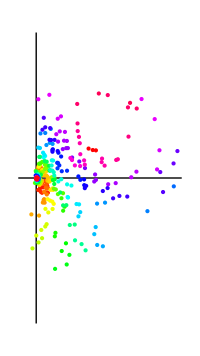

```mathematica
vizHandmap2[
rfs,
DisplayTracts->All,
ImageSize->200,
VirtualTracts->None,
PolygonCenterMarkers->True,
PolygonCenterConnectors->False,
PolygonCenterConnectorStyle->Thickness[0.001],
HidePolygons->True,
CoordIndex0->3,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree}
]
```